# Sprott #12

The ODE is
	y'''[t]==-0.5y''[t]-y'[t]+y[t]-Sign[y[t]]
It (and it’s companion #11) are not quite smooth enough for our standard “Lipschitz” existence and uniqueness theorem!  This was addressed in a lecture. For now we are just going to approximate the solution numerically.

### 3rd Order ODE

The natural way to solve the 3rd order ODE in Mathematica.  The corners in the solution are directly from the jump in “Sign”.

```mathematica
TMax=123;
ySol=NDSolveValue[{
y'''[t]==-0.5y''[t]-y'[t]+y[t]-Sign[y[t]],
y[0]==0,
y'[0]==1,
y''[0]==0}, y,{t,0, TMax}];
TabView[{
"y, y', y'' vs t"->Plot[{ySol[t],ySol'[t],ySol''[t]},{t,0, TMax}],
"Phase Plot"->ParametricPlot3D[{ySol[t],ySol'[t],ySol''[t]},{t,0, TMax},
PlotRange->All,
PlotPoints->100]
}]
```

12

### 1st Order ODE System

We can write this as a first order system for the vector w=(y
v
a)  where y=y, v=y', and a=v'=y''.
	(y
v
a)'=(y'
v'
a')=(v
a
y''')=(v
a
-0.5 a-v+y -Sign[y])
The cell below defines a function and solve the ODE as the first order system
	w'=f(w)
If I want different colors I need to

```mathematica
Clear[w]
TMax=123;
f[{y_,v_,a_}]:= {v,a, -0.5 a-v+y -Sign[y]}
wSol= NDSolveValue[ {w'[t]==f[w[t]],w[0]=={0,1,0}},w,{t,0,TMax}];
TabView[{
"Phase Plot"->ParametricPlot3D[wSol[t],{t,0, TMax},PlotPoints->100],
"w vs t"->Plot[{wSol[t][[1]],wSol[t][[2]],wSol[t][[3]]},{t,0, TMax},PlotPoints->100,
PlotLegends->Automatic,
AxesLabel->{"t"," "}]
}]
```

12

### 1st Order ODE System with Parameters

The default #12 ODE is 
	(y_1
y_2
y_3)'=(y_2
y_3
-0.5 y_3-y_2+y_1 -Sign[y_1])
I am going to add parameters a, b, c, and d in the last equation. For convenience I am going to pass the parameters at the front of the function.  The default values of the parameters are going to be {a,b,c,d}={0.5,1,1,1}.  The function is 
	f[{a,b,c,d}][{y_1,y_2,y_3}]=(y_2
y_3
-a y_3-b y_2+c y_1 -d Sign[y_1]) 
The function is defined below. The first test has the default parameters called p0.  The second has nearby parameters called p1.

```mathematica
Clear[f,w]
f[{a_,b_,c_,d_}][{y1_,y2_,y3_}]:= {y2,y3, -a y3-b y2+c y1 -d Sign[y1]}
p0={0.5,1,1,1};
p1={0.5,1,1,0.9};
TMax=123;
y0={0,1,0};
ySol0= NDSolveValue[ {y'[t]==f[p0][y[t]],y[0]==y0},y,{t,0,TMax}];
ySol1= NDSolveValue[ {y'[t]==f[p1][y[t]],y[0]==y0},y,{t,0,TMax}];
ParametricPlot3D[{ySol0[t],ySol1[t]},{t,0, TMax},
PlotLegends->{"p0","p1"},
AxesLabel->{"y_1","y_2","y_3"},
PlotLabel->"Sprott #12"]
```

-Graphics3D-

### Smooth Parameterized 1st Order ODE System with J=∇_x y

Our function is not smooth enough for our J trick! I am going to cheat and replace the non-smooth term with a smoothed out variant.

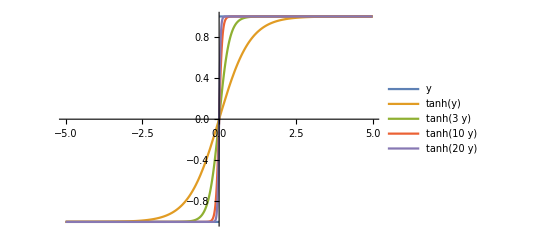

```mathematica
Plot[{Sign[y],Tanh[y],Tanh[3y],Tanh[10 y],Tanh[20y]},{y,-5,5},
PlotLegends->"Expressions"]
```

Our smoothed function is 
	f({y_1,y_2,y_3})=(y_2
y_3
-a y_3-b y_2+c y_1 -d tanh(m y_1)) 
Differentiate y'=f(y)  and y(0)=x with respect to x to get
	∇_x y'=df(y) ∇_x y and ∇_x y(0)=∇_x x=I_3
where the 3×3 derivative of f with respect to y is 
	df({y_1,y_2,y_3})=(0 | 1 | 0
0 | 0 | 1
c - d m sech^2(m y) | -b | -a).
The ODE for the sensitivity matrix J=∇_x y  
	J'=df(y) J and J(0)=I_3
naturally contains a matrix-matrix product.  I am going to add “m” to the parameter list and pick a default value of 30.

```mathematica
Clear[f,w]
f[{a_,b_,c_,d_,m_}][{y1_,y2_,y3_}]:= {y2,y3, -a y3-b y2+c y1 -d Tanh[m y1]}
df[{a_,b_,c_,d_,m_}][{y1_,y2_,y3_}]:= ({{0, 1, 0}, {0, 0, 1}, {c - d m Sech[m y1]^2, -b, -a}})
p0={0.5,1,1,1,30};
p1={0.5,1,1,0.9,30};
TMax=123;
y0={0,1,0};
J0=IdentityMatrix[3];
{ySol0,JSol0}= NDSolveValue[ {
y'[t]==f[p0][y[t]],
J'[t]==df[p0][y[t]].J[t],
y[0]==y0,J[0]==J0},{y,J},{t,0,TMax}];
{ySol1,JSol1}= NDSolveValue[ {
y'[t]==f[p1][y[t]],
J'[t]==df[p1][y[t]].J[t],
y[0]==y0,J[0]==J0},{y,J},{t,0,TMax}];
ParametricPlot3D[{ySol0[t],ySol1[t]},{t,0, TMax},
PlotLegends->{"p0","p1"},
AxesLabel->{"y_1","y_2","y_3"},
PlotLabel->"Smoothed Sprott #12"]
MatrixForm[JSol0[1.0]]
SingularValueList[JSol0[1.0]]
```

-Graphics3D-

(0.757996 | 0.88618 | 0.399559
-0.286167 | 0.726573 | 0.694636
0.288307 | -0.30482 | 0.394618)

{1.42995,0.773279,0.548524}

As expected one of the singular values goes to zero!  The flow is compressing a direction.

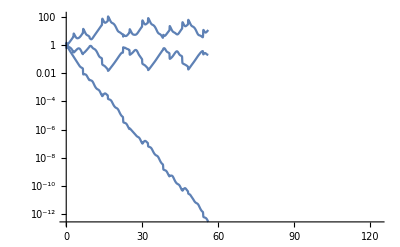

```mathematica
LogPlot[SingularValueList[JSol0[t]],{t,0, TMax}]
```

To save a graph: Name the graph, choose the directory (if you click on Insert/File Path you get a familiar browser)  you want, and export the graph to whatever format (defined by the file extension) you want.

```mathematica
Pic=ParametricPlot3D[{ySol0[t],ySol1[t]},{t,0, TMax},
PlotLegends->{"p0","p1"},
AxesLabel->{"y_1","y_2","y_3"},
PlotLabel->"Smoothed Sprott #12"];
SetDirectory["C:\\Users\\AllanStruthers\\Desktop"]
Export["AASPic.jpg",Pic]
```

C:\Users\AllanStruthers\Desktop

AASPic.jpg

### Smooth System with J=∇_x y and S=D_params y

We can differentiate our smoothed function
	f({y_1,y_2,y_3})=(y_2
y_3
-a y_3-b y_2+c y_1 -d tanh(m y_1)) 
with respect to a,b,c, and d to get
	dpf({y_1,y_2,y_3})=(0 | 0 | 0 | 0
0 | 0 | 0 | 0
-y_3 | -y_2 | y_1 | -tanh(m y_1)) .
The first column is the derivative with respect to a, the second column is the derivative with respect to b, the third column the derivative with respect to c, and the third column the derivative with respect to d.  The 3×4 matrix  
	S=[∂_a y,∂_b y,∂_c y,∂_d y]
is the sensitivity of the solution y with respect to the parameters p={a,b,c,d}.  Differentiating y'=f(y) with respect to a gives
	∂_a y'=∂_a (y_2
y_3
-a y_3-b y_2+c y_1 -d tanh(m y_1))=(∂_a y_2
∂_a y_3
-y_3-a ∂_a y_3-b ∂_a y_2+c ∂_a y_1 -d m sech^2(m y_1)∂_a y_1).
Differentiating with respect to b gives
	∂_b y'=∂_b (y_2
y_3
-a y_3-b y_2+c y_1 -d tanh(m y_1))=(∂_b y_2
∂_b y_3
-a ∂_b y_3-y_2-b ∂_b y_2+c ∂_b y_1 -d m sech^2(m y_1)∂_b y_1).
Differentiating with respect to c gives
	∂_c y'=∂_c (y_2
y_3
-a y_3-b y_2+c y_1 -d tanh(m y_1))=(∂_c y_2
∂_c y_3
-a ∂_c y_3-b ∂_c y_2+y_1+c ∂_c y_1 -d m sech^2(m y_1)∂_c y_1).
Finally, differentiating with respect to d gives
	∂_d y'=∂_d (y_2
y_3
-a y_3-b y_2+c y_1 -d tanh(m y_1))=(∂_d y_2
∂_d y_3
-a ∂_d y_3-b ∂_d y_2+c ∂_d y_1 -d m sech^2(m y_1)∂_d y_1-tanh(m y_1)).
We can assemble this to get
	[∂_a y | ∂_b y | ∂_c y | ∂_d y]'=(0 | 0 | 0 | 0
0 | 0 | 0 | 0
-a y_3 | -b y_2 | c y_1 | -d tanh(m y_1))+(0 | 1 | 0
0 | 0 | 1
c - d m sech^2(m y) | -b | -a).[∂_a y | ∂_b y | ∂_c y | ∂_d y]
which is simply
	S'=dpf(y)+df(y) S
for the 3×4 parameter sensitivity matrix for the solution y on the parameters.  The initial condition does not depend on the parameters so we initialize with 
	 S(0)=0_(3×4)

```mathematica
Clear[f,w]
f[{a_,b_,c_,d_,m_}][{y1_,y2_,y3_}]:= {y2,y3, -a y3-b y2+c y1 -d Tanh[m y1]}
df[{a_,b_,c_,d_,m_}][{y1_,y2_,y3_}]:= ({{0, 1, 0}, {0, 0, 1}, {c - d m Sech[m y1]^2, -b, -a}})
dpf[{a_,b_,c_,d_,m_}][{y1_,y2_,y3_}]:=({{0, 0, 0, 0}, {0, 0, 0, 0}, {-y3, -y2, y1, -Tanh[m y1]}})
p0={0.5,1,1,1,30};
p1={0.5,1,1,0.9,30};
TMax=123;
y0={0,1,0};
J0=IdentityMatrix[3];
S0=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
{ySol0,JSol0,SSol0}= NDSolveValue[ {
y'[t]==f[p0][y[t]],
J'[t]==df[p0][y[t]].J[t],
S'[t]==dpf[p0][y[t]]+df[p0][y[t]].S[t],
y[0]==y0,J[0]==J0,S[0]==S0},{y,J,S},{t,0,TMax}];
```

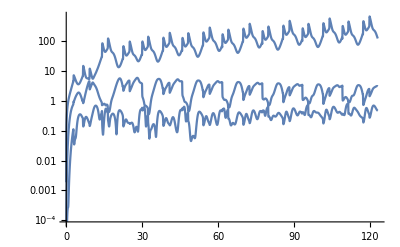

```mathematica
LogPlot[SingularValueList[SSol0[t]],{t,0,TMax}]
```